```mathematica
ParticleFiltering[X_,M_,E_,n_,e_]:=
(*This algo here is an MCMC filtering, where single samples are evolved according to the model; the result lies in the relative frequence, for every realization, of the values in the returned vector. The support of the variables is always N+, so that we can easily index the matrixes; X is a stochastic vector representing the a-priori distribution;
 M=P(Xt+1|Xt) is the transition (eg: (TT,FT;TF,FF) and I have M[1,2]=P(Xt+1=F|Xt=T)) as a regular stochastic matrix on the rows;
E=P(Et|Xt) the sensorial (eg: supra E[2,1]=P(Et=T|Xt=F)); 
n the number of particles; 
e the evidence*)

Module[{
values=Table[i,{i,1,Length[X]}],
(*poniamo come supporto di X l'insieme N+, per poter indicizzare agevolmente le matrici*) 
generations={}
},
Module[{
particles=RandomChoice[X->values,n],
(*generating the particles from the a priori distribution, which represents the weights for the RandomChoice function*)
weights=ConstantArray[1/n,n],
(*pesi iniziali (potremmo anche farne a meno)*)
(*initial weights (we could also do without)*)
i,j
},
AppendTo[generations,particles];
For[i=1,i≤Length[e],i++,
For[j=1,j≤n,j++,
particles[[j]]=RandomChoice[M[[particles[[j]],All]]->values];
(*let's take the row of the M matrix corresponding to the particle value, e sample one of such values: this is extracting a particle, checking what realization is it and seek to the corresponding row on M; to evolve the particle it means selecting a new value at the next instant t+1 based on the row itself, which represents the possible translations*)
weights[[j]]=E[[e[[i]],particles[[j]]]]
(*analogously, the weights come from the sensor matrix*)
];
particles=RandomChoice[weights->particles,Length[particles]];
AppendTo[generations,particles]
(*weighted sample with replacement: the aim is to refresh the popolation of particles by randomly selecting, according to their weights, members from the current population*)
];
generations
]
]
```

```mathematica
ParticleFiltering[{.5,.5},{{.7,.3},{.3,.7}},{{.2,.8},{.8,.2}},500,RandomChoice[{1,2},50]]
```

{«1»}

```mathematica
trail[M_,m_,points_]:=If[m==0,points,trail[M,m-1,Append[points,RandomChoice[M[[Last[points],All]]->{1,2}]]]]
```

```mathematica
states=trail[{{.7,.3},{.3,.7}},50,RandomChoice[{1,2},1]];
```

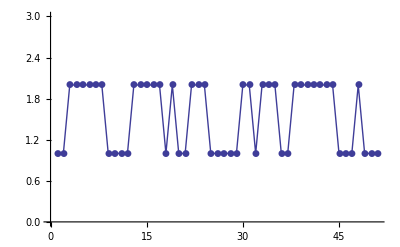

```mathematica
ListPlot[states,PlotRange->{0,3},Joined->True,PlotMarkers->Automatic]
```

```mathematica
(*try and compare this with the predicted trail, what do you expect?*)
```